# Investigating the relationship between Gini index and well-being

Neofytos Themistokleous

## Introduction

Inspired by the results of social epidemiologist Richard Wilkinsonm, I decided to try and replicate some of his work using the Wolfram Language. More specifically, some of his claims that are shown in this YouTube video : https : // www.youtube.com/watch?v = aOUJbV66Nm4 . My speculation is that the Gini index of an area will be inversely proportional to quantities of social well - being.

First of all. What is the Gini index? Let’ s ask the Wolfram Language :

```mathematica
EntityValue[EntityProperty["AdministrativeDivision","GiniIndex"],"Definition"]
```

The extent to which the distribution of income among individuals or households within an economy deviates from a perfectly equal distribution. A Lorenz curve plots the cumulative percentages of total income received against the cumulative number of recipients, starting with the poorest individual or household. The Gini index measures the area between the Lorenz curve and a hypothetical line of absolute equality, expressed as a fraction of the maximum area under the line. Thus a Gini index of 0 represents perfect equality, while an index of 1 implies perfect inequality.

So, simply put, it is the measurement of social inequality in an area

## Implementation Decisions

First of all, which geographical areas should be added to our analysis? It was decided to work on all the US states. Some of the data are not available for European countries or US state subdivisions.

```mathematica
usstates=EntityList[EntityClass["AdministrativeDivision","ContinentalUSStates"]];
```

```mathematica
usstates[[5;;10]]
```

{Colorado, United States,Connecticut, United States,Delaware, United States,Florida, United States,Georgia, United States,Idaho, United States}

Now, how does one measure wellbeing though? The "AdministrativeDivision" provides plenty of options that can be seen by running :

```mathematica
EntityProperties["AdministrativeDivision"];
```

After having a look at them, I chose the following ones to use, based on the predictions of Richard Wilkinsonm and my intuition :

```mathematica
allentities = {EntityProperty["AdministrativeDivision","GiniIndex"],EntityProperty["AdministrativeDivision","Businesses"],EntityProperty["AdministrativeDivision","CrimeRate"],EntityProperty["AdministrativeDivision","DisabledPersons"],EntityProperty["AdministrativeDivision","AnnualDeaths"],EntityProperty["AdministrativeDivision","HealthInsuranceUncoveredRate"],EntityProperty["AdministrativeDivision","HomeOwnershipRate"],EntityProperty["AdministrativeDivision","MinimumWage"],EntityProperty["AdministrativeDivision","TotalVotingRate"],EntityProperty["AdministrativeDivision","CivilianUnemploymentRate"]} ;
```

A list of names for those quantities is also created for use further down the road:

```mathematica
names = CommonName@allentities
```

{Gini index,number of businesses,total rate of crime,disabled people,annual deaths,uninsured population fraction,home ownership rate,minimum wage,total voting rate,civilian unemployment rate}

## Acquiring & preparing the data

It is about time to get the data. Luckily, Thread and AssociationThread make requesting the data and passing them to a Dataset a one-liner command.

```mathematica
data=AssociationThread[names->QuantityMagnitude@Thread[EntityValue[usstates, allentities]]] // Dataset;
```

Some of the selected variables : number of businesses, disabled people, and annual deaths are not normalised. To normalised them :

```mathematica
normalisedbusiness=(data["number of businesses"]//Normal)/(QuantityMagnitude@Thread[EntityValue[usstates, EntityProperty["AdministrativeDivision","Population"]]])*100;
```

```mathematica
normaliseddeaths =(data["annual deaths"]//Normal)/(QuantityMagnitude@Thread[EntityValue[usstates, EntityProperty["AdministrativeDivision","Population"]]])*100;
```

```mathematica
normaliseddisabled =(data["disabled people"]//Normal)/(QuantityMagnitude@Thread[EntityValue[usstates, EntityProperty["AdministrativeDivision","Population"]]])*100//N;
```

```mathematica
data=ReplacePart[data,"number of businesses"->normalisedbusiness];
```

```mathematica
data=ReplacePart[data,"annual deaths"->normaliseddeaths];
```

```mathematica
data=ReplacePart[data,"disabled people"->normaliseddisabled];
```

Let' s have a look the resulting dataset :

```mathematica
data
```

Dataset[<>]

The above is an association of lists. It is suitable for the analysis that will take place, but as can be seen above, it is harder to visualise.

```mathematica
Data  analysis & Visualisation
```

Having the data in the appropriate format, it is about time to look for correlations between them and the Gini index. Initially a fit is performed between Gini index and all the other quantities individually.

```mathematica
fits= Table[Fit[Transpose@{Normal@data["Gini index"],Normal@data[names[[i]]]},{1,x},x],{i,Length[names]}];
```

A table of plots is created, showing the data points for each correlation, together with the fitted line

```mathematica
plots=ArrayReshape[Table[ListPlot[Transpose@{Normal@data["Gini index"],Normal@data[names[[i]]]},AxesLabel->{"Gini index",names[[i]]}],{i,Length[names]}],{5,2}];
```

```mathematica
plots=ArrayReshape[
Table[
Show[
ListPlot[Transpose@{Normal@data["Gini index"],Normal@data[names[[i]]]},AxesLabel->{"Gini index",names[[i]]}],
Plot[fits[[i]],{x,0.425,0.55}]]
,{i,Length[names]}]
,{5,2}];
```

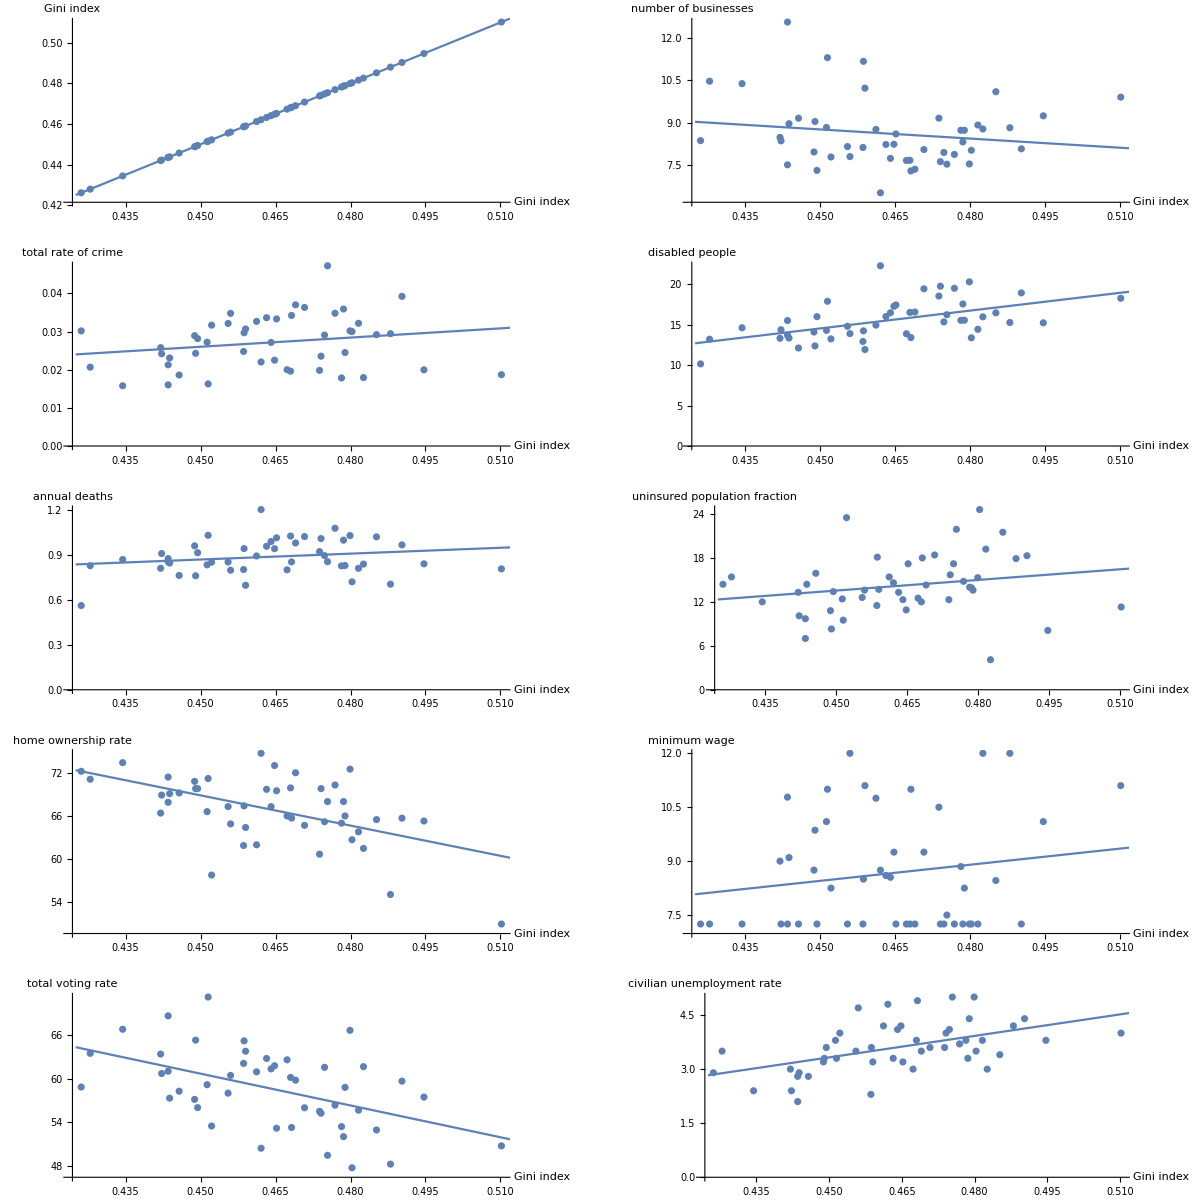

```mathematica
GraphicsGrid[plots,ImageSize->{1200,1200}]
```

Some patterns can be spotted from the plots, but there is a way to quantify that using the Correlation function. The function give the Pearson’ s correlation coefficient to vectors

```mathematica
correlations=Reverse@SortBy[Abs[#[[3]]]&]@Table[{EntityProperty["AdministrativeDivision","GiniIndex"],allentities[[i]],Correlation[Normal@data["Gini index"],Normal@data[names[[i]]]]},{i,Length[names]}];
```

```mathematica
correlations//Column
```

{Gini index,Gini index,1.}
{Gini index,home ownership rate,-0.532003}
{Gini index,disabled people,0.529797}
{Gini index,civilian unemployment rate,0.506169}
{Gini index,total voting rate,-0.485893}
{Gini index,uninsured population fraction,0.210305}
{Gini index,total rate of crime,0.203853}
{Gini index,annual deaths,0.202066}
{Gini index,minimum wage,0.167087}
{Gini index,number of businesses,-0.16282}

Conclusions :
 Some correlations were found, but not the ones expected. This may be due to a number of reasons ...

```mathematica
(* More discussion will be added, but not code *)
```